In the following explanations:
w_t - wages at time t
r_t - return on capital at time t
C_t - consumption at time t
L_t - labour at time t
K_t- capital at time t
I_t - investment at time t
Y_t  - output at time t
(K^f)_t - firms choice of capital at time t
(L^f)_t - firms choice of labour at time t
Π_t - profits at time t
(Π^f)_t - firm profits at time t
δ - depreciation of capital
A - level of technology
α - Capital income share

```mathematica
Question 2
```

```mathematica
(*The 'Score' function calculates the utility until consumption has reached a steady state. Then, as consumption is constant, use a geometric series to sum the remaining values to infinity. Given that by maximising household utility we solve the model, the Household utility function acts as the fitness score in this genetic algorithm*)
score[Cvalues_,T_,beta_,additionalPeriods_]:=Module[

(*Local Variables*)
{utility1,utility2,utility},

(*Using the household function (as described in Question 1), we can calculate utility from T=0, up until the steady state of capital has been achieved. 'Additional periods' represents the number of periods it takes for constant savings rates to create a consumption steady state*)
utility1=Sum[(beta^t)*Log[Cvalues[[t+1]]],{t,0,T+additionalPeriods}];

(*Once constant consumption has been reached, the remaining terms in the series until ∞ can be calculated using the sum to infinity property of geometric series as |β|<1, satisfying the condition*)
(*Log(C^*)*β^(T+additionalPeriods+1)/(1-β)*)
utility2=Log[Cvalues[[T+additionalPeriods]]]*beta^(T+additionalPeriods+1)/(1-beta);

(*Summing utility from T=0 until the steady state of consumption, with the remaining period until infinity, we have total utility)*)
utility=utility1+utility2;

(*Return total utility (Fitness score)*)
utility]


(*The 'CreateInitialChromosome' function is called iteratively by the main code to generate the starting population. Each chromosome consists of a random guess of savings until T=70. After T=70, the savings steady state is reached, and the series is extended for some 'additionalPeriods', constant at the steady state, to allow for the steady state of consumption to be achieved*)
CreateInitialChromosome[T_,A_,delta_,alpha_,initialCapital_,additionalPeriods_]:=Module[

(*Local Variables*)
{firstGuesses,totalGuesses},

(*Generate random guesses for T periods, accommodating for mathematica indexing from 1*)
firstGuesses=RandomReal[{0.0001,0.9999},T+1];

(*'Join' the first T periods to a constant array of the savings steady state, extended by enough 'additionalPeriods' such that consumption can reach its steady state*)
totalGuesses=Join[firstGuesses,ConstantArray[firstGuesses[[-1]],additionalPeriods]];

(*Using the savings rate, generate the chromosome's Consumption series*)
chromosomeGenerator[T,A,delta,alpha,initialCapital,totalGuesses,False,additionalPeriods]];



(*The 'chromosomeGenerator' function generates accompanying series for C, K, I and Y given parameters and a series of savings rates. The parameter 'all' determines whether the function returns a multi-dimensional list containing all 5 series or only savings and consumption.*)
chromosomeGenerator[T_,A_,delta_,alpha_,initialCapital_,sValues_,all_,additionalPeriods_]:=Module[

(*Local Variables*)
{capital,output,consumption,investment,t},

(*Initialize lists to store the calculated values of K, Y, C, and I. The length of these lists is T+1+additionalPeriods. T+1 accounts for periods indexed from 1 instead of 0,and T+1+additionalPeriods includes additional periods to allow consumption to reach its steady states.*)
capital=ConstantArray[0,T+1+additionalPeriods];
output=ConstantArray[0,T+1+additionalPeriods];
consumption=ConstantArray[0,T+1+additionalPeriods];
investment=ConstantArray[0,T+1+additionalPeriods];

(*Place the initial value of K as the first entry in the capital series.*)
capital[[1]]=initialCapital;

(*Use the production function Y=K^α A^(1-α) to calculate initial output, Y.*)
output[[1]]=capital[[1]]^alpha*A^(1-alpha);

(*Investment is the share of output that is saved, not consumed. Calculate initial investment, Subscript[I, t] = Subscript[s, t] Subscript[Y, t].*)
investment[[1]]=sValues[[1]]*output[[1]];

(*The remaining fraction of output is used for consumption. Calculate initial consumption, (1-Subscript[s, t])Subscript[Y, t]=C.*)
consumption[[1]]=(1-sValues[[1]])*output[[1]];

(*Iterate through remaining periods to calculate K, Y, C,and I. Start from T=1 (indexed at 2 in Mathematica) until the final period when consumptions has reached its steady state.*)
For[t=2,t<=T+additionalPeriods+1,t++,

(*Update capital: Subscript[K, t]=(1-δ)Subscript[K, t-1] + Subscript[I, t-1]*)
capital[[t]]=(1-delta)*capital[[t-1]]+investment[[t-1]];

(*Update output: Y=K^α A^(1-α)*)
output[[t]]=capital[[t]]^alpha*A^(1-alpha);

(*Update investment: Subscript[I, t] = Subscript[s, t] Subscript[Y, t]*)
investment[[t]]=sValues[[t]]*output[[t]];

(*Update consumption:Cₜ=(1-sₜ)Yₜ.*)
consumption[[t]]=(1-sValues[[t]])*output[[t]];];

(*Return savings and consumption if 'all' is False; otherwise, return all variables. This allows the function to have dual-functionality increasing reusability*)
If[all==False,Return[{sValues,consumption}],Return[{sValues,consumption,capital,investment,output}]]];



(*The 'SelectionGen' function evaluates the fitness of each chromosome in the population using the 'score' function. By choosing which chromosomes become parents and which are dropped, it returns the top 50% of the population based on fitness.*)
selectionGen[population_,T_,beta_,additionalPeriods_]:=Module[

(*Local Variables*)
{fitnessScores,halfLength,sortedIndexes,survivorPop,topFitnessScores},

(*Apply the score function to each chromosome in the population using 'Map'. The fitness score is based on consumption (second list of each population entity).*)
fitnessScores=Map[score[#[[2]],T,beta,additionalPeriods]&,population];

(*Determine the number of solutions to retain (50% of the population).Using 'Ceiling' accommodates for the population size to be something other than a multiple of 4. If the population size is 4n or 4n+1, the population will stay of constant size in all generations. If it is 4n+2 or 4n+3,the next generation will have a population size of 4(n+1),and remain constant from there.*)
halfLength=Ceiling[Length[fitnessScores]/2];

(*Sort indexes of the highest-scoring chromosomes in descending order. This ensures the fittest solutions have higher ranks, ideal when later implementing rank-probability for breeding.*)
sortedIndexes=Ordering[fitnessScores,-halfLength];

(*Create a sublist of the population with the highest-scoring members.*)
survivorPop=population[[sortedIndexes]];

(*Keep fitness scores for the surviving population to track score evolution.*)
topFitnessScores=fitnessScores[[sortedIndexes]];

(*Return a multidimensional list containing savings, consumption, and fitness scores of the surviving population. We do this using 'MapThread', similar to 'Map', but applies the function to multiple lists, automatically aligning indexes*)
MapThread[Join[#1,{{#2}}]&,{survivorPop,topFitnessScores}]];



(*The 'parentsGen' function selects which chromosomes become parents given their fitness score, and pairs them up. It uses rank-based probability to give higher fitness solutions a better chance of being selected.*)
parentsGen[survivorPop_]:=Module[

(*Local Variables*)
{ranks,probabilities},

(*Assign ranks to the population based on their order (higher index = better fitness). We make use of the fact the surviving chromosomes are sorted in descending order*)
ranks=Range[Length[survivorPop]];

(*Normalize ranks to sum to 1, creating a probability distribution for selection.*)
probabilities=ranks/Total[ranks];

(*Generate pairs of solutions for breeding using pseudorandom selection based on probabilities. Given that each pair produces two chromosomes, we create 'n/2' pairs to replace 'n' discarded chromosomes. Using 'Table', we iterate through the survivors, using 'RandomSample' which given a set of probabilities and associated values, creates pairs with replacements, which are then returned. By using RandomSample, we prevent the irregularity of a solution breeding with itself.*)
Table[RandomSample[probabilities->survivorPop,2],{Length[survivorPop]/2}]];



(*The 'decimalToBinary' function converts a decimal number to a binary floating-point representation. Default precision is 14 bits,sufficient for numbers between 0 and 1 up to 4 decimal places accurately. It is assumed all savings rates are between 0 and 1*)
decimalToBinary[decimal_,precision_:14]:=Module[

(*Local Variables*)
{fraction=decimal,digits},

(*Generate binary digits with the specified precision. Iterating using 'Table', we multiply the decimal value by 2, shifting it one place to the left in binary. If the result of the doubling creates a value greater than 1, then we add a '1' to our binary string, and subtract 1 from the decimal value. If doubling does not make the decimal value exceed 1, we add a '0' to our binary string. We repeat until we reach the given level of precision*)
digits=Table[If[(fraction=2*fraction)>=1,fraction-=1;"1","0"],{precision}];

(*Return binary representation with "0." prepended to indicate it is less than 1.*)
"0."<>StringJoin[digits]];



(*The 'generateSolutions' function iteratively calls 'crossover' for each breeding-pair*) 
generateSolutions[binaryData_,mutationRate_]:=Module[

(*Local Variables*)
{offspring},

(*Using 'Table' apply the 'crossover' function to each pair, creating new chromosomes.*)
offspring=Table[crossover[binaryData[[j]],mutationRate],{j,Length[binaryData]}];

(*Flatten the pairs of new chromosomes into a single population and return.*)
Flatten[offspring,1]];



(*The 'crossover' function creates child chromosomes from parent chromosomes. Each pair of chromosome's are split at a random point, and the halves are recombined to form 2 child chromosomes. Mutations are also applied.*)
crossover[couple_,mutationRate_]:=Module[

(*Local Variables: split each pair into parent 1 and parent 2*)
{parent1=couple[[1]],parent2=couple[[2]],offspring1,offspring2,maxSplitPos,splitPos,string1,string2},

(*Determine the possible split positions. We do not split before the floating point, as all solutions being less than 1 will mean this has no effect. Splitting at the last point to create children identical to parents is acceptable.*)
maxSplitPos=StringLength[StringDrop[parent1[[1]],2]];

(*Select a pseudorandom point where the chromosomes will be split*)
splitPos=RandomInteger[{1,maxSplitPos}];

(*To create the first chromosome, we use 'Table' to iterate through all savings rates*)
offspring1=Table[

(*We remove the '0.' prefix as applying a mutation to this bit would create a savings rate that exceeds 1*)
string1=StringDrop[parent1[[i]],2];
string2=StringDrop[parent2[[i]],2];

(*The first chromosome is from the from the first part of parent one, and the second part of parent two, dictated by the split position. The 'mutateChromosome' function applies any possible mutations, and '0.' is reattached.*)
"0."<>mutateChromosome[StringTake[string1,splitPos]<>StringDrop[string2,splitPos],mutationRate],{i,Length[parent1]}];

(*Generate the second chromosomes in a similar manner to the first, instead taking the first part of parent two, and the second part of parent one.*)
offspring2=Table[string1=StringDrop[parent1[[i]],2];
string2=StringDrop[parent2[[i]],2];
"0."<>mutateChromosome[StringTake[string2,splitPos]<>StringDrop[string1,splitPos],mutationRate],{i,Length[parent2]}];

(*Return the child chromosomes created from parent chromosomes*)
{offspring1,offspring2}];



(*The 'mutateChromosome' function applies bit-flipping mutations to a chromosome based on the mutation rate, mutating the children*)
mutateChromosome[bitString_,mutationRate_]:=Module[

(*Local Variables: Split the string into individual bits.*)
{bits=Characters[bitString],flippedBits},

(*To the list of bits we apply a set of rules that will consider mutating each bit according to the mutation rate*)
flippedBits=bits/. {

(*For each bit, generate a pseudorandom number between 0 and 1. If that number is less than the mutation rate then apply a bit-flipping mutation (0->1 / 1->0). There is an x% chance the randomly generated number is below the mutation rate, x, and a (1-x)% chance it is above*)
"0":>If[RandomReal[]<mutationRate,"1","0"],
"1":>If[RandomReal[]<mutationRate,"0","1"]};

(*Combine mutated bits back into a string and return.*)
StringJoin[flippedBits]];



(*The 'binaryToDecimal' function converts a binary floating-point string back to a decimal value.*)
binaryToDecimal[binaryString_]:=Module[

(*Local Variables: Remove "0." from binary string.*)
{fraction=StringDrop[binaryString,2],decimal=0,i},

(*Iterate through each binary digit and calculate its contribution to the decimal value.*)
For[i=1,i<=StringLength[fraction],i++,

(*Convert each bit to a decimal value by multiply it by 2^-i, where i is the distance from the floating point. Summing these values creates the full decimal expression*)
decimal+=ToExpression[StringTake[fraction,{i}]]*2.^(-i)];

(*Return the decimal value.*)
N[decimal]];
```

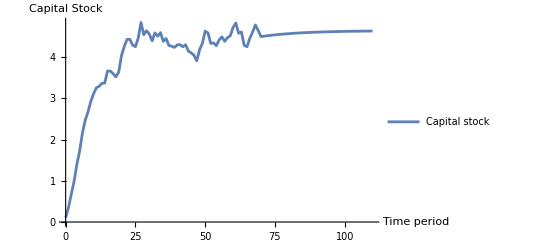

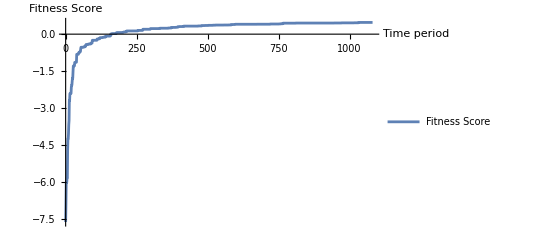

```mathematica
(*Define key parameters as specified in the problem statement. Greek letters are written in their full names due to the constraint of using symbols as arguements*)
A=1; 
delta=0.1; 
alpha=0.33; 
beta=0.98; 
initialCapital=0.1; 
T=70; 

(*The code accommodates population sizes that are not multiples of 4*)
populationSize=80; 
mutationRate=0.025; 

(*Minimum number of generations*)
generations=1000; 

(*Maximum number of generations*)
maximumGenerations=2000;

(*To simulate steady-state convergence, the savings rate is kept constant after T periods,allowing consumption and other variables to stabilize. 'additionalPeriods' specifies how many extra periods are required.*)
additionalPeriods=40;

(*After the minimum number of generations, if the fitness score is constant for so many periods, we assume no more progress to be made.*)
consecutivePeriods = 50;

(*An array to store the best solution from each generation, helpful for tracking evolution.*)
bestsolution={};

(*Main Body*)

(*Using 'Table', generate the initial population of chromosomes. Each chromosome will contain a savings rate series and consumption series. Further generations will be a combination of surviving parents and new offspring.*)
population=Table[CreateInitialChromosome[T,A,delta,alpha,initialCapital,additionalPeriods],{populationSize}];

(*Start loop counter*)
i=1; 

(*Perform the genetic algorithm for at least 'generations' loops. Then if there has been enough 'consecutivePeriods' where the fitness score has not changed, the code will stop. Otherwise the code will run until the 'maximumGenerations' are reached*)
While[

(*The Loop will always run for at least the number of required generations*)
i<=generations||

(*The loop will continue beyond the minimum number of generations if it has not exceeded the maximum number of generations AND*)
(i<=maximumGenerations&&

 (*The minimum number of periods for the fitness score to converge has not been reached*)
(Length[bestsolution]<consecutivePeriods||

(*OR the last fitness score has not been constant for long enough,indicating the solution is still improving. The ‘Union’ function counts how many unique fitness scores have been recorded in the previous periods. If this exceeds 1, it means the solution is still improving*)
Length[Union[bestsolution[[-consecutivePeriods;;,3,1]]]]>1)),


(*Select the top 50% of the population based on fitness scores to act as parents.*)
survivorPop=selectionGen[population,T,beta,additionalPeriods];

(*The last entry in the sorted survivor population has the highest fitness score. Track this chromosome for monitoring the evolution of the best solution.*)
AppendTo[bestsolution,survivorPop[[Length[survivorPop]]]];

(*If we have reached the final generation, there is no need to create a new population as there are no further generations.*)
If[

(*The same conditions as in the while loop*)
i<=generations||(i<=maximumGenerations&&(Length[bestsolution]<consecutivePeriods||Length[Union[bestsolution[[-consecutivePeriods;;,3,1]]]]>1)),

(*Generate pairs of chromosomes for breeding.*)
pairs=parentsGen[survivorPop];

(*Using 'Map', we apply a function that extracts the savings rate from each parent chromosome.From this point onwards we do not need the consumption series or the fitness score, so removing them promotes efficiency*)parentsSaving=Map[{#[[1,1]],#[[2,1]]}&,pairs];

(*Trim the savings rate series to exclude the additional periods used for steady-state convergence to promotes efficiency. These are no longer needed.*)
parentsSavingT=

(*The outer'Map' applies the inner function to all pairs of parents, the inner 'Map' applies the function to each individual pair*)
Map[Map[

(*To the list of savings,'Take' the savings rates'upTo' the steady state of savings,excluding all additionalPeriods*)
Take[#,UpTo[Length[#]-additionalPeriods]]&,#]&,parentsSaving];

(*Convert the trimmed savings rates to binary representations.*)
binaryData=Map[decimalToBinary,parentsSavingT,{3}];

(*Create child chromosomes using the binary data and the mutation rate.*)
children=generateSolutions[binaryData,mutationRate];

(*Convert the binary offspring chromosomes back to decimal format.The function is applied using a'Map' at level 3 (the function is applied to a list containing pairs of lists)*)
decodedSolutions=Map[binaryToDecimal,children,{2}];

(*For the purposes of scoring in the next generation,extend each child chromosomes by the 'additionalPeriods' required for consumption to reach its steady state. We use 'Map' to 'Join' the savings rates with a constant array containing each chromosomes steady state savings rate for every additional period required for consumption convergence*)
extendedChildren=Map[Join[#,ConstantArray[Last[#],additionalPeriods]]&,decodedSolutions];

(*Combine surviving parents and new children to form the next generation's population.From the surviving parents we extract only the savings rate data*)
newPop=Join[extendedChildren,survivorPop[[All,1]]];

(*Using'Table',we generate consumption values for the new population via their savings rates.In the event the new population is not the same size as the previous generation due to the initial population size being divisible by 4 (split into the top 50% and then reproduced using breeding-pairs),we continue on with an adjusted population size,at most 1 chromosome bigger or smaller*)
population=Table[chromosomeGenerator[T,A,delta,alpha,initialCapital,newPop[[i]],False,additionalPeriods],{i,Length[newPop]}];

(*Increment loop counter*)
i++; 

]
]

(*Use the 'chromosomeGenerator' function with 'all=True' to retrieve the fittest chromosome's full series of savings, consumption, capital, investment, and output. Given that the fittest chromosomes always survives to the next generation, the final value in the 'bestSolution' array will contain the highest scoring chromosome*)
variables=chromosomeGenerator[T,A,delta,alpha,initialCapital,bestsolution[[Length[bestsolution]]][[1]],True,additionalPeriods];

(*We can split variables into sublists, i.e, s, C, K, I, Y*)
savingGenetic = variables[[1]];
consumptionGenetic = variables[[2]];

(*Given that in the competitive equilibrium Household allocation of capital is equal to firm allocation of capital,our capital stock solves for both values*)
capitalstockGenetic = variables[[3]];
investmentGenetic = variables[[4]];
outputGenetic= variables[[5]];

(*Using the first order conditions from part 1 we can derive vectors for wages and returns on capital *)
wageGenetic=(1-alpha)*(capitalstockGenetic/A)^alpha*A;
returnGenetic=alpha*(A/capitalstockGenetic)^(1-alpha);

(*Plot the evolution of capital stock over time for the best solution.*)
ListPlot[

(*Mathematica indexes lists from 1, but our periods start from T=0. We use 'Table' to subtract 1 from each index,ensuring our graph accurately plots the data.*)
Table[{t,capitalstockGenetic[[t+1]]},{t,0,Length[capitalstockGenetic]-1}],

(*Graph settings, including range, axis labels, and legend*)
Joined->True,PlotRange->All,AxesLabel->{"Time period","Capital Stock"}, PlotLegends->Placed[{"Capital stock"},Below]]

(*Extract the fitness scores of the best solutions from each generation. These are stored in the first list of each chromosome, in the first position*)
FitnessScores=bestsolution[[All,3,1]];

(*Plot the evolution of fitness scores across generations.*)
ListPlot[

(*Mathematica indexes lists from 1, but our periods start from T=0. We use 'Table' to subtract 1 from each index,ensuring our graph accurately plots the data.*)
Table[{t,FitnessScores[[t+1]]},{t,0,Length[FitnessScores]-1}],

(*Graph settings, including range, axis labels, and legend*)
Joined->True,PlotRange->All,AxesLabel->{"Time period","Fitness Score"}, PlotLegends->Placed[{"Fitness Score"},Below]]
```